# Release from L5PN synapses

#### Last update: HS Aug. 2025, for PFC coupling project: Use according to settings determined by Ca data fit Status: Influx via different Cav driven by AP waveform; multiple APs with unitstep function Buffering by cooperative CR and CR B5 with FF, ATP, EGTA or BAPTA, slow and fast endogenous buffers with estimted kinetics New Syt1 sensor models instead of Syt2 models Concentrations in mol/m3 (i.e. factor 10^-3 gives mol/l or mol/l * 10^3 = mol/m3)

## Edit

```mathematica
(*General settings*)
shells=400;                                (*1 based indexing; 1 is inner shell*)

APN=1;
ISI=20.*10^-3;
LF=0.7; (*loading factor for pipette loading or for AM chelator loading according to Baur et al., J Neurosci, 2015*)

longAP=0;


young=0;
younglAP=0;
adult=1;

If[APN≤1,
TimeWindow=0.002,
TimeWindow=APN*ISI];

DiscreteDist=0;
(*DistList={22,23, 24};*)
DistList={7};
(*DistList={45,46, 47};*)

CaRest =  29.*10^-6; (*10^-9/10^-3; i.e. 103 nM*)
FF=0.2;                (*IF of CR in innermost shell*)

(*Chelator settings*)
native=1;                                  (*native = 1 removes EGTA/BAPTA*)
low=1;                                       (*1 = EGTA, 0 = BAPTA*)


cEGTA=10.*10^0*LF;             (*i.e. 10 mM * LF; 2.*10^-3 as endogenous buffer; cf L5PN Ca fit*)
cBAPTA=10.*10^0;

(*Plotting & Calculating*)
FusPlot=1;
CaPlot=1;
AvCaPlot=1;
CalPr=1;
CalPPR=0;
CumPlot=0;
CalCaList=0;


(*Buffer capacity; used to calculate concentrations of unknown edogenous buffers*)

κS=25;           (*120, 25, 7*)   (*140 in Koester & Sakmann, J Physiol, 2000; kappa fix =100 in CA1, Matthews et al., J Neurosci, 2013; 50% wash out assumed; Tran & Stricker, Biophys J, 2018; L5PN boutons; kappa 7 or 25, no mobile buffers*)

(*CAVE: Don't forget changegin fix buffer settings for different kappaS: FSB = 0 for kappaS of 7 and 25!*)

kOffFBscale=1; (*0.1, 1, 10*)
FSB=0.07;     (*fraction of slow EB; 0, 0.07, 0.1; or 0 for kappaS of 7 and 25*)
FFB=1-FSB;     (*fraction of fast EB*)
FFSB=0.5;  (*fixed fraction of SB*)
FFFB=0.5;    (*fixed fraction of FB*)


(*AP and Cav and Pump*)
(*young; normal AP*)

(*young, different kappaS*)
If[young==1,
If[κS==120,
NPQ=12;
NN=7;  
NR=0;
NL=0;];

If[κS==25,
NPQ=7;
NN=5;  
NR=0;
NL=0;];

If[κS==7,
NPQ=6;
NN=4;  
NR=0;
NL=0;];
];


(*young; long AP*)
If[younglAP==1,
NPQ=6.5;
NN=3;  
NR=0;
NL=0;]

(*adult*)
If[adult==1,
NPQ=8;
NN=0;  (*N make no contribution to release in adult according to the data*)
NR=0;
NL=0;]

ECa=130*10^-3;
Vrest=-80*10^-3;
γ=3.2*10^-4;                (*pumprate 1/s; gamma is the free parameter*)
```

## Geometry & Constants

```mathematica
(*Vb=0.127*10^-18 m^3; Schikorski & Stevens, PNAS, 1999; olfactory cortex; corrected for space occupied by vesicles and organelles, factor 0.635 (Wilhelm et al., Science, 2014): 0.2 * 0.635*)

DCa =220 *10^-12;    (*DiffCo; m2/s*)
NA = 6.022*10^23;  (*Teilchen/mol; Avogadros Number*)
F=96485.;    (*C/mol; Farraday*)

ClearAll[Vs,As]

r=0.4*10^-6;    

ds = r/shells;
Vs[0]=0;
As[0]=0;
For[i=1,i≤shells,i++,     Vs[i]=2/3*π*(i*ds)^3-2/3*π*((i-1)*ds)^3     (*;Print[Vs[i]]  *) ](*hemi-spheres; in m3*)
For[i=1,i≤shells,i++,     As[i]=2*π*(i*ds)^2 ]
(*hemi-spheres; in m^2*)


VsTotal =2/3*π*(shells*ds)^3;
(*Print[Test V," =  ",VsTotal,  " =  ",∑_(s=1)^shells (Vs[s])]
Print["spatial resolution = ", ds, "m"]*)
```

## Influx

### Action potential and Ca channels

#### APs: Unitstep with Double Exp Function

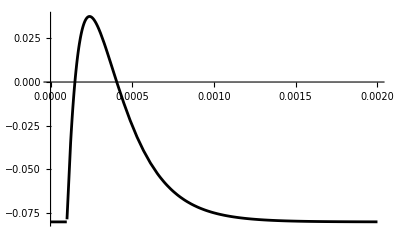

```mathematica
Clear[Vm,startT,taud,taur]
startT=0.1*10^-3;
taur=0.1*10^-3;

If[longAP==1,
taud=0.4*10^-3,
taud=0.2*10^-3];


Vm=Sum[(UnitStep[t-i]*(Exp[-(t-i)/taud]-Exp[-(t-i)/taur])),{i,startT,startT+(APN-1)*ISI,ISI}];

If[longAP==1,
Vm=0.25*Vm-0.08,
Vm=0.47*Vm-0.08];


plAP=Plot[Vm,{t,0,TimeWindow},PlotRange->All,PlotStyle->Black]
```

#### P/Q type channel

(Li et al., J Neurosci, 2007; cf. Ermolyuk et al., Nat Neurosci, 2013 and Scimemi et al., J Neurosci, 2012)

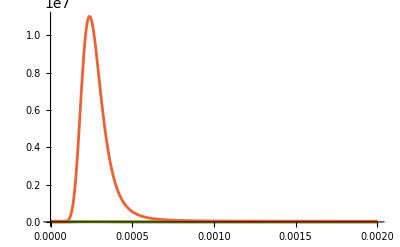

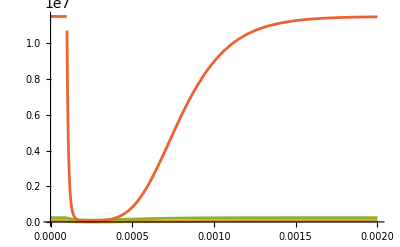

```mathematica
Clear[α,Α,β,Β]

gPQ=2.5*10^-12;   (*pS; assumed values as in the above papers*)

α[1]=5.89*10^3;
α[2]=9.21*10^3;
α[3]=5.2*10^3;
α[4]=1823.18*10^3;
Α=247.71*10^3;

β[1]=14.99*10^3;
β[2]=6.63*10^3;
β[3]=132.8*10^3;
β[4]=248.58*10^3;
Β=8.28*10^3;

k[1]=62.61*10^-3;
k[2]=33.92*10^-3;
k[3]=135.08*10^-3;
k[4]=20.86*10^-3;

Table[alpha[i]=α[i] Exp[Vm/k[i]],{i,1,4}];
Table[beta[i]=β[i] Exp[-Vm/k[i]],{i,1,4}];

Plot[{alpha[1],alpha[2],alpha[3],alpha[4]},{t,0,TimeWindow},PlotRange->All]
Plot[{beta[1],beta[2],beta[3],beta[4]},{t,0,TimeWindow},PlotRange->All]
```

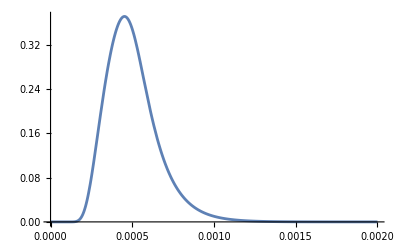

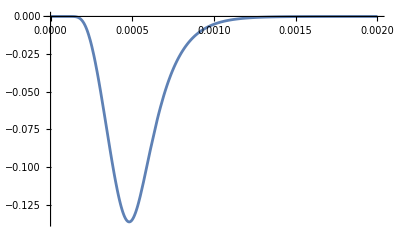

```mathematica
PQChannel={
PQCh0[0]==1,
PQCh1[0]==0,
PQCh2[0]==0,
PQCh3[0]==0,
PQCh4[0]==0,
PQChOpen[0]==0,

PQCh0'[t]==-PQCh0[t]*alpha[1]+PQCh1[t]*beta[1],

PQCh1'[t]==-PQCh0'[t]-PQCh1[t]*alpha[2]+PQCh2[t]*beta[2],

PQCh2'[t]==PQCh1[t]*alpha[2]-PQCh2[t]*beta[2]-PQCh2[t]*alpha[3]+PQCh3[t]*beta[3],

PQCh3'[t]==PQCh2[t]*alpha[3]-PQCh3[t]*beta[3]-PQCh3[t]*alpha[4]+PQCh4[t]*beta[4],

PQCh4'[t]==PQCh3[t]*alpha[4]-PQCh4[t]*beta[4]-PQCh4[t]*Α+PQChOpen[t]*Β,

PQChOpen'[t]==PQCh4[t]*Α-PQChOpen[t]*Β};



VarsPQ={PQCh0,PQCh1,PQCh2,PQCh3,PQCh4,PQChOpen};

solPQ:=NDSolve[PQChannel,VarsPQ,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{PQChOpen[t]}/.solPQ],{t,0,TimeWindow},PlotRange->All]

Plot[Evaluate[10^12*gPQ*(Vm-ECa)*{PQChOpen[t]}/.solPQ],{t,0,TimeWindow},PlotRange->{0,-0.15}]
```

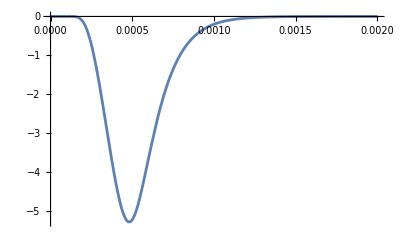

{{0.00187387}}

{{151.258}}

```mathematica
InfluxPQ:=(1/(2   F*Vs[1]))*gPQ*(Vm-ECa)*PQChOpen[t]

InPQ:=Evaluate[(1/(2*F* VsTotal))*gPQ*(Vm-ECa)*{PQChOpen[t]}/.solPQ]
Plot[InPQ,{t,0,TimeWindow},PlotRange->All]
conc=NIntegrate[-InPQ,{t,0,TimeWindow}]
CaIons=conc*NA*VsTotal
```

#### N type channel

(Li et al., J Neurosci, 2007; cf. Ermolyuk et al., Nat Neurosci, 2013 and Scimemi et al., J Neurosci, 2012)

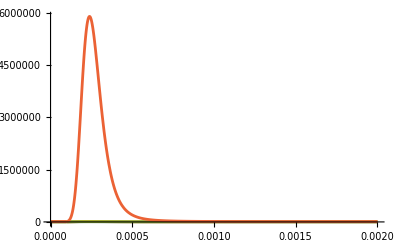

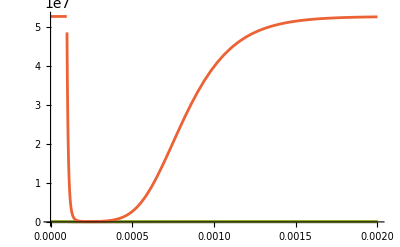

```mathematica
Clear[αN,ΑN,βN,ΒN]

gN=2.5*10^-12;

αN[1]=4.29*10^3;
αN[2]=5.24*10^3;
αN[3]=4.98*10^3;
αN[4]=772.63*10^3;
ΑN=615.01*10^3;

βN[1]=5.23*10^3;
βN[2]=6.63*10^3;
βN[3]=73.89*10^3;
βN[4]=692.18*10^3;
ΒN=7.68*10^3;

kN[1]=68.75*10^-3;
kN[2]=39.53*10^-3;
kN[3]=281.62*10^-3;
kN[4]=18.46*10^-3;

Table[alphaN[i]=αN[i] Exp[Vm/kN[i]],{i,1,4}];
Table[betaN[i]=βN[i] Exp[-Vm/kN[i]],{i,1,4}];

Plot[{alphaN[1],alphaN[2],alphaN[3],alphaN[4]},{t,0,TimeWindow},PlotRange->All]
Plot[{betaN[1],betaN[2],betaN[3],betaN[4]},{t,0,TimeWindow},PlotRange->All]
```

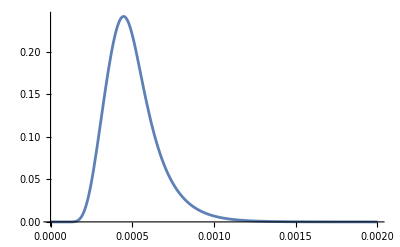

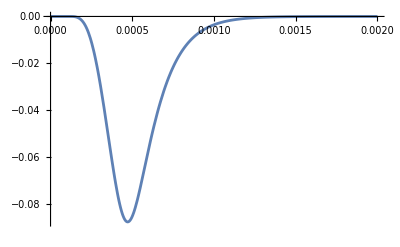

```mathematica
NChannel={
NCh0[0]==1,
NCh1[0]==0,
NCh2[0]==0,
NCh3[0]==0,
NCh4[0]==0,
NChOpen[0]==0,

NCh0'[t]==-NCh0[t]*alphaN[1]+NCh1[t]*betaN[1],

NCh1'[t]==-NCh0'[t]-NCh1[t]*alphaN[2]+NCh2[t]*betaN[2],

NCh2'[t]==NCh1[t]*alphaN[2]-NCh2[t]*betaN[2]-NCh2[t]*alphaN[3]+NCh3[t]*betaN[3],

NCh3'[t]==NCh2[t]*alphaN[3]-NCh3[t]*betaN[3]-NCh3[t]*alphaN[4]+NCh4[t]*betaN[4],

NCh4'[t]==NCh3[t]*alphaN[4]-NCh4[t]*betaN[4]-NCh4[t]*ΑN+NChOpen[t]*ΒN,

NChOpen'[t]==NCh4[t]*ΑN-NChOpen[t]*ΒN};



VarsN:={NCh0,NCh1,NCh2,NCh3,NCh4,NChOpen}

solN:=NDSolve[NChannel,VarsN,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{NChOpen[t]}/.solN],{t,0,TimeWindow},PlotRange->All]

Plot[Evaluate[10^12*gN*(Vm-ECa)*{NChOpen[t]}/.solN],{t,0,TimeWindow},PlotRange->{0,-0.15}]
```

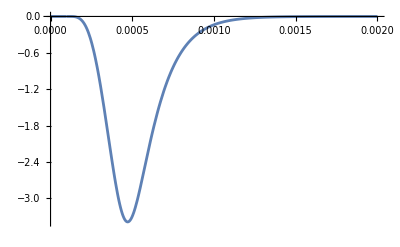

{{0.00117156}}

{{94.5677}}

```mathematica
InfluxN:=(1/(2 F  Vs[1]))*gN*(Vm-ECa)*NChOpen[t]

InN:=Evaluate[(1/(2 F  VsTotal))*gN*(Vm-ECa)*{NChOpen[t]}/.solN]
Plot[InN,{t,0,TimeWindow},PlotRange->All]
concN=NIntegrate[-InN,{t,0,TimeWindow}]
CaIonsN=concN*NA*VsTotal
```

#### R type channel

(Li et al., J Neurosci, 2007; cf. Ermolyuk et al., Nat Neurosci, 2013 and Scimemi et al., J Neurosci, 2012)

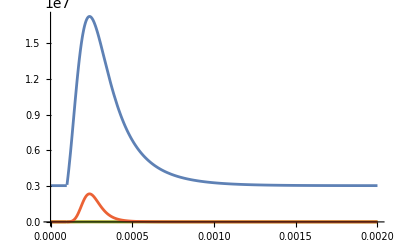

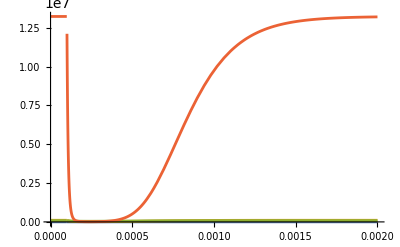

```mathematica
Clear[αR,ΑR,βR,ΒR]

gR=2.5*10^-12;

αR[1]=9911.36*10^3;
αR[2]=4.88*10^3;
αR[3]=4*10^3;
αR[4]=256.41*10^3;
ΑR=228.83*10^3;

βR[1]=0.62*10^3;
βR[2]=21.91*10^3;
βR[3]=51.3*10^3;
βR[4]=116.97*10^3;
ΒR=1.78*10^3;

kR[1]=67.75*10^-3;
kR[2]=50.94*10^-3;
kR[3]=173.29*10^-3;
kR[4]=16.92*10^-3;

Table[alphaR[i]=αR[i] Exp[Vm/kR[i]],{i,1,4}];
Table[betaR[i]=βR[i] Exp[-Vm/kR[i]],{i,1,4}];

Plot[{alphaR[1],alphaR[2],alphaR[3],alphaR[4]},{t,0,TimeWindow},PlotRange->All]
Plot[{betaR[1],betaR[2],betaR[3],betaR[4]},{t,0,TimeWindow},PlotRange->All]
```

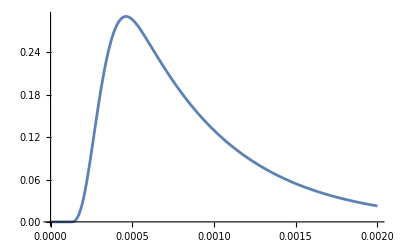

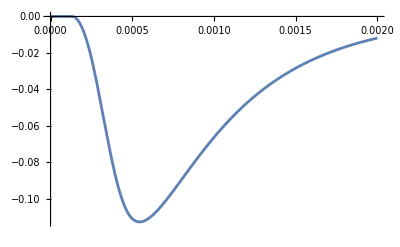

```mathematica
RChannel={
RCh0[0]==1,
RCh1[0]==0,
RCh2[0]==0,
RCh3[0]==0,
RCh4[0]==0,
RChOpen[0]==0,

RCh0'[t]==-RCh0[t]*alphaR[1]+RCh1[t]*betaR[1],

RCh1'[t]==-RCh0'[t]-RCh1[t]*alphaR[2]+RCh2[t]*betaR[2],

RCh2'[t]==RCh1[t]*alphaR[2]-RCh2[t]*betaR[2]-RCh2[t]*alphaR[3]+RCh3[t]*betaR[3],

RCh3'[t]==RCh2[t]*alphaR[3]-RCh3[t]*betaR[3]-RCh3[t]*alphaR[4]+RCh4[t]*betaR[4],

RCh4'[t]==RCh3[t]*alphaR[4]-RCh4[t]*betaR[4]-RCh4[t]*ΑR+RChOpen[t]*ΒR,

RChOpen'[t]==RCh4[t]*ΑR-RChOpen[t]*ΒR};



VarsR:={RCh0,RCh1,RCh2,RCh3,RCh4,RChOpen}

solR:=NDSolve[RChannel,VarsR,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{RChOpen[t]}/.solR],{t,0,TimeWindow},PlotRange->All]

Plot[Evaluate[10^12*gR(Vm-ECa)*{RChOpen[t]}/.solR],{t,0,TimeWindow},PlotRange->{0,-0.15}]
```

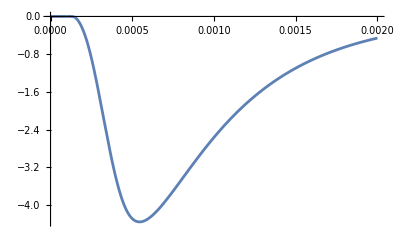

{{0.00380757}}

{{307.346}}

```mathematica
InfluxR:=(1/(2 F  Vs[1]))*gR*(Vm-ECa)*RChOpen[t]

InR:=Evaluate[(1/(2 F  VsTotal))*gR*(Vm-ECa)*{RChOpen[t]}/.solR]
Plot[InR,{t,0,TimeWindow},PlotRange->All]
concR=NIntegrate[-InR,{t,0,TimeWindow}]
CaIonsR=concR*NA*VsTotal
```

#### L type channel simple

(Beyl et al., J Gen Physiol, 2009)

```mathematica
Clear[αL,ΑL,βL,ΒL]

gL=9.*10^-12;   (*von Wegner & Fink, Eur Biophys J, 2010.*)

αL=0.427*10^3;
ΑL=0.15*10^3;

βL=0.216*10^3;
ΒL=0.24*10^3;

kLa=328.8*10^-3;
kLb=9.04*10^-3;

alphaL=αL Exp[Vm/kLa];
betaL=βL Exp[-Vm/kLb];
```

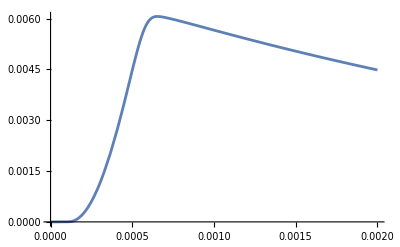

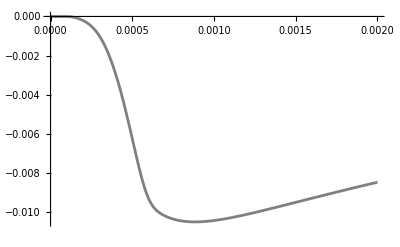

```mathematica
LChannel={
LCh0[0]==1,
LCh1[0]==0,
LChOpen[0]==0,

LCh0'[t]==-LCh0[t]*alphaL+LCh1[t]*betaL,

LCh1'[t]==-LCh0'[t]-LCh1[t]*ΑL+LChOpen[t]*ΒL,

LChOpen'[t]==LCh1[t]*ΑL-LChOpen[t]*ΒL};


VarsL:={LCh0,LCh1,LChOpen}

solL:=NDSolve[LChannel,VarsL,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{LChOpen[t]}/.solL],{t,0,TimeWindow},PlotRange->All]

plL=Plot[Evaluate[10^12*gL(Vm-ECa)*{LChOpen[t]}/.solL],{t,0,TimeWindow},PlotRange->{0,-0.15},PlotStyle->Gray]
```

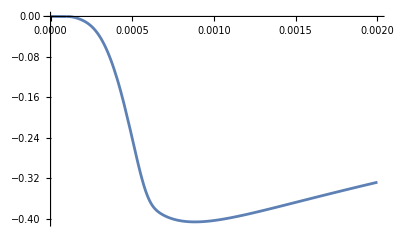

{{0.000583908}}

{{47.1328}}

```mathematica
InfluxL:=(1/(2 F VsTotal))*gL*(Vm-ECa)*LChOpen[t]
InL:=Evaluate[(1/(2 F VsTotal))*gL*(Vm-ECa)*{LChOpen[t]}/.solL]
Plot[InL,{t,0,TimeWindow},PlotRange->All]
concL=NIntegrate[-InL,{t,0,TimeWindow}]
CaIonsL=concL*NA*VsTotal
```

## Buffering

### EGTA or BAPTA

EGTA / BAPTA kinetics
Naraghi, 1997; Nägerl, 2000; Eggermann & Jonas, 2012

```mathematica
OGtotal =If[native==1,0,If[low==1, cEGTA,cBAPTA]] ;

kOnOG  = If[low==1, 1.0*10^4,4.0*10^5];     (*Values from Nägerl et al., 2000*)
kOffOG = If[low==1,0.7,88.];               
KdOG =kOffOG/kOnOG
DOG = 220.*10^-12;


kappaOG=OGtotal/KdOG

RestOG=OGtotal/(CaRest/KdOG+1.);
RestCaOG= OGtotal - RestOG;



BufferOG=Join[
(* t=0 equations *)
Table[OG[i][0]==RestOG,{i,1,shells}],
Table[{CaOG[i][0]==RestCaOG},{i,1,shells}],

(* f' equations for shell1 *)
{OG[1]'[t]==-kOnOG*Ca[1][t]* OG[1][t]+ kOffOG *CaOG[1][t]
+ DOG *As[1]/(Vs[1]*ds)*(OG[2][t]-OG[1][t])},

{CaOG[1]'[t]==kOnOG*Ca[1][t]* OG[1][t]- kOffOG *CaOG[1][t]- DOG *As[1]/(Vs[1]*ds)*(CaOG[1][t]-CaOG[2][t])},

(* f' equations for 2 to shells-1 *)
Table[
{OG[i]'[t]==-kOnOG*Ca[i][t]* OG[i][t]- DOG *As[i-1]/(Vs[i]*ds)*(OG[i][t]-OG[i-1][t])+ kOffOG *CaOG[i][t]
+ DOG *As[i]/(Vs[i]*ds)*(OG[i+1][t]-OG[i][t])},{i,2,shells-1}],
Table[
{CaOG[i]'[t]==kOnOG*Ca[i][t]* OG[i][t]+ DOG *As[i-1]/(Vs[i]*ds)*(CaOG[i-1][t]-CaOG[i][t])- kOffOG *CaOG[i][t]- DOG *As[i]/(Vs[i]*ds)*(CaOG[i][t]-CaOG[i+1][t])},{i,2,shells-1}],

(* f' equations for outermost shell *)

{OG[shells]'[t]==-kOnOG*Ca[shells][t]* OG[shells][t]+ kOffOG *CaOG[shells][t]
- DOG *As[shells-1]/(Vs[shells]*ds)*(OG[shells][t]-OG[shells-1][t])},

{CaOG[shells]'[t]==kOnOG*Ca[shells][t]* OG[shells][t]- kOffOG *CaOG[shells][t]+ DOG*As[shells-1]/(Vs[shells]*ds)*(CaOG[shells-1][t]-CaOG[shells][t])}

];

BufferOG = Flatten[BufferOG];
```

0.00007

0.

### ATP

```mathematica
ATPtotal = 600.*10^-3 ;(*total free pipette concentration*)(*90% of free pipette concentration of 600 µM =540 µM Kd Mg = 100 µM => only ~ 64 ATP free;      anything between 64 and 600 goes!*)    
DATP = 220.*10^-12;                                        (*Meinrencken et al., 2002;*)
kOnATP  = 5*10^5;
kOffATP = 100000.;
KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP

RestATP=ATPtotal/(CaRest/KdATP+1.);
RestCaATP= ATPtotal - RestATP;
```

3.

#### Buffer equations ATP

```mathematica
BufferATP=Join[
(* t=0 equations *)
Table[ATP[i][0]==RestATP,{i,1,shells}],
Table[CaATP[i][0]==RestCaATP,{i,1,shells}],

(* f' equations for shell1 *)
{ATP[1]'[t]==-kOnATP*Ca[1][t]* ATP[1][t]+ kOffATP *CaATP[1][t]
+ DATP *As[1]/(Vs[1]*ds)*(ATP[2][t]-ATP[1][t])},

{CaATP[1]'[t]==kOnATP*Ca[1][t]* ATP[1][t]- kOffATP *CaATP[1][t]- DATP *As[1]/(Vs[1]*ds)*(CaATP[1][t]-CaATP[2][t])},

(* f' equations for 2 to shells-1 *)
Table[
{ATP[i]'[t]==-kOnATP*Ca[i][t]* ATP[i][t]- DATP *As[i-1]/(Vs[i]*ds)*(ATP[i][t]-ATP[i-1][t])+ kOffATP *CaATP[i][t]
+ DATP *As[i]/(Vs[i]*ds)*(ATP[i+1][t]-ATP[i][t])},{i,2,shells-1}],
Table[
{CaATP[i]'[t]==kOnATP*Ca[i][t]* ATP[i][t]+ DATP *As[i-1]/(Vs[i]*ds)*(CaATP[i-1][t]-CaATP[i][t])- kOffATP *CaATP[i][t]- DATP *As[i]/(Vs[i]*ds)*(CaATP[i][t]-CaATP[i+1][t])},{i,2,shells-1}],

(* f' equations for outermost shell *)

{ATP[shells]'[t]==-kOnATP*Ca[shells][t]* ATP[shells][t]+ kOffATP *CaATP[shells][t]
- DATP *As[shells-1]/(Vs[shells]*ds)*(ATP[shells][t]-ATP[shells-1][t])},

{CaATP[shells]'[t]==kOnATP*Ca[shells][t]* ATP[shells][t]- kOffATP *CaATP[shells][t]+ DATP*As[shells-1]/(Vs[shells]*ds)*(CaATP[shells-1][t]-CaATP[shells][t])}

];


BufferATP = Flatten[BufferATP];
```

### CR

```mathematica
CRtotal =0.*10^-3;
                                
CRBVtotal =0.*10^-3;
              

DCR = 20*10^-12 ;

kOnT=1.8*10^3;
kOffT=53.;   
KdT = kOffT/kOnT;

kOnR=3.1*10^5;
kOffR=20.;   
KdR = kOffR/kOnR;

kOnCRapp = √(kOnT*kOnR)        ;
kOffCRapp = √(kOffT*kOffR)        ;
KdCRapp = kOffCRapp /kOnCRapp ;

(*independent BS V*)
kOnBV=5.*10^5;
kOffBV=5000.;   
KdCRBV = kOffBV/kOnBV;

kappCR=0.5 CRtotal/KdCRapp;
kappaR=CRtotal/KdR;
kappaT=CRtotal/KdT;
kappaBV=CRBVtotal/KdCRBV
```

0.

#### Resting conditions for CR

```mathematica
RestCRBV=CRBVtotal/(CaRest/KdCRBV+1.);
RestCaCRBV= CRBVtotal - RestCRBV;

RuheCR=Join[
(* t=0 equations *)
{RestCR[0]==CRtotal},
{RestCaCR[0]==0},
{RestCa2CR[0]==0},

(* f' equations *)
{RestCR'[x]==-(RestCaCR'[x]+RestCa2CR'[x])},
{RestCaCR'[x]==2*kOnT*CaRest* RestCR[x] - kOffT *RestCaCR[x]-kOnR*CaRest* RestCaCR[x] + 2*kOffR *RestCa2CR[x]},
{RestCa2CR'[x]==kOnR*CaRest* RestCaCR[x] - 2*kOffR *RestCa2CR[x]}

];

solCR := NDSolve[RuheCR,{RestCR,RestCaCR,RestCa2CR},{x,0.,1.}]; 

(*Plot[Evaluate[{10^6*RestCaCR[x]/.solCR,10^6*RestCa2CR[x]/.solCR,10^6*RestCR[x]/.solCR},{x,0.,1.}],PlotRange->All,AxesLabel->µM,PlotLabel->"Synapse, CaCR"]*)

IniCR = Extract[RestCR[1.]/.solCR,1];
IniCaCR = Extract[RestCaCR[1.]/.solCR,1];
IniCa2CR = Extract[RestCa2CR[1.]/.solCR,1];
```

#### Buffer equations CR

```mathematica
BufferCR=Join[
(* t=0 equations *)
Table[{CR[i][0]==IniCR},{i,1,shells}],
Table[{CaCR[i][0]==IniCaCR},{i,1,shells}],
Table[{Ca2CR[i][0]==IniCa2CR},{i,1,shells}],

(* f' equations for shell1 *)
{CR[1]'[t]==-2*kOnT*Ca[1][t]* CR[1][t] + kOffT *CaCR[1][t]
+(1-FF) DCR *As[1]/(Vs[1]*ds)*(CR[2][t]-CR[1][t])},
{CaCR[1]'[t]==2*kOnT*Ca[1][t]* CR[1][t] - kOffT *CaCR[1][t]
-kOnR*Ca[1][t]* CaCR[1][t] + 2*kOffR *Ca2CR[1][t]
-(1-FF) DCR *As[1]/(Vs[1]*ds)*(CaCR[1][t]-CaCR[2][t])},
{Ca2CR[1]'[t]==kOnR*Ca[1][t]* CaCR[1][t] - 2*kOffR *Ca2CR[1][t]
-(1-FF) DCR *As[1]/(Vs[1]*ds)*(Ca2CR[1][t]-Ca2CR[2][t])},


(* f' equations for 2 to shells-1 *)
Table[
{CR[i]'[t]==-2*kOnT*Ca[i][t]* CR[i][t] + kOffT *CaCR[i][t]
+(1-FF) DCR *As[i]/(Vs[i]*ds)*(CR[i+1][t]-CR[i][t])
-(1-FF)DCR *As[i-1]/(Vs[i]*ds)*(CR[i][t]-CR[i-1][t])},{i,2,shells-1}],
Table[
{CaCR[i]'[t]==2*kOnT*Ca[i][t]* CR[i][t] - kOffT *CaCR[i][t]
-kOnR*Ca[i][t]* CaCR[i][t] + 2*kOffR *Ca2CR[i][t]
+(1-FF)DCR *As[i-1]/(Vs[i]*ds)*(CaCR[i-1][t]-CaCR[i][t])
-(1-FF)DCR *As[i]/(Vs[i]*ds)*(CaCR[i][t]-CaCR[i+1][t])},{i,2,shells-1}],
Table[
{Ca2CR[i]'[t]==kOnR*Ca[i][t]* CaCR[i][t] - 2*kOffR *Ca2CR[i][t]
+(1-FF)DCR *As[i-1]/(Vs[i]*ds)*(Ca2CR[i-1][t]-Ca2CR[i][t])
-(1-FF)DCR *As[i]/(Vs[i]*ds)*(Ca2CR[i][t]-Ca2CR[i+1][t])},
{i,2,shells-1}],


(* f' equations for outermost shell *)
{CR[shells]'[t]==-2*kOnT*Ca[shells][t]* CR[shells][t] +kOffT *CaCR[shells][t]
-(1-FF)DCR *As[shells-1]/(Vs[shells]*ds)*(CR[shells][t]-CR[shells-1][t])},
{CaCR[shells]'[t]==2*kOnT*Ca[shells][t]* CR[shells][t] - kOffT *CaCR[shells][t]
-kOnR*Ca[shells][t]* CaCR[shells][t] +2*kOffR *Ca2CR[shells][t]
+(1-FF)DCR *As[shells-1]/(Vs[shells]*ds)*(CaCR[shells-1][t]-CaCR[shells][t])},
{Ca2CR[shells]'[t]==kOnR*Ca[shells][t]* CaCR[shells][t] - 2*kOffR *Ca2CR[shells][t]
+(1-FF)DCR *As[shells-1]/(Vs[shells]*ds)*(Ca2CR[shells-1][t]-Ca2CR[shells][t])}
];
BufferCR = Flatten[BufferCR];

BufferBV=Join[
(* t=0 equations *)
Table[CRBV[i][0]==RestCRBV,{i,1,shells}],
Table[CaCRBV[i][0]==RestCaCRBV,{i,1,shells}],

(* f' equations for shell1 *)
{CRBV[1]'[t]==-kOnBV*Ca[1][t]* CRBV[1][t]+ kOffBV *CaCRBV[1][t]
+ (1-FF)*DCR *As[1]/(Vs[1]*ds)*(CRBV[2][t]-CRBV[1][t])},

{CaCRBV[1]'[t]==kOnBV*Ca[1][t]* CRBV[1][t]- kOffBV *CaCRBV[1][t]- DCR *As[1]/(Vs[1]*ds)*(CaCRBV[1][t]-CaCRBV[2][t])},

(* f' equations for 2 to shells-1 *)
Table[
{CRBV[i]'[t]==-kOnBV*Ca[i][t]* CRBV[i][t]-(1-FF)* DCR *As[i-1]/(Vs[i]*ds)*(CRBV[i][t]-CRBV[i-1][t])+ kOffBV *CaCRBV[i][t]
+ (1-FF)*DCR *As[i]/(Vs[i]*ds)*(CRBV[i+1][t]-CRBV[i][t])},{i,2,shells-1}],
Table[
{CaCRBV[i]'[t]==kOnBV*Ca[i][t]* CRBV[i][t]+(1-FF)* DCR *As[i-1]/(Vs[i]*ds)*(CaCRBV[i-1][t]-CaCRBV[i][t])- kOffBV *CaCRBV[i][t]-(1-FF)* DCR *As[i]/(Vs[i]*ds)*(CaCRBV[i][t]-CaCRBV[i+1][t])},{i,2,shells-1}],

(* f' equations for outermost shell *)

{CRBV[shells]'[t]==-kOnBV*Ca[shells][t]* CRBV[shells][t]+ kOffBV *CaCRBV[shells][t]
-(1-FF)* DCR *As[shells-1]/(Vs[shells]*ds)*(CRBV[shells][t]-CRBV[shells-1][t])},

{CaCRBV[shells]'[t]==kOnBV*Ca[shells][t]* CRBV[shells][t]- kOffBV *CaCRBV[shells][t]+ (1-FF)*DCR*As[shells-1]/(Vs[shells]*ds)*(CaCRBV[shells-1][t]-CaCRBV[shells][t])}

];

BufferBV = Flatten[BufferBV];
```

### Unknown slow endogenous buffer

L5PNs do not express large amounts of EB with known kinetics (Celio, Neurosci, 1990; Baimbridge et al., TINS, 1992); therefore, unknonwn EB is assumed; Assumptions: EGTA-like slow binding kinetics (biphasic Ca Signal, Lee et al., J Physiol, 2000, Schmidt et al., J Physiol, 2003);

```mathematica
DSB=0.*10^-12; (*buffers have no substantial mobility in L5PNs; Helmchen et al., Biophys J, 1996*)
                                        
kOnSB  = 1.*10^4;(*Naraghi, 1997:2.6*10^6, 0.468; Nägerl et al., 2000: 1*10^7; 0.7; Kd 70 nM*)
kOffSB = 0.7;
KdSB = kOffSB/kOnSB;
10^6*KdSB;

SBtotal = κS*FSB*KdSB (*Calculated from kappaS*)
kappaSB=SBtotal/KdSB;

RestSB=SBtotal/(CaRest/KdSB+1.);
RestCaSB= SBtotal - RestSB;

Print["KdSB (nM) ", 10^6*KdSB]
Print["conc. SB (µM) ", SBtotal*1000]
Print["kappa SB ", kappaSB]
```

0.0001225

KdSB (nM) 70.

conc. SB (µM) 0.1225

kappa SB 1.75

#### Buffer equations SB

```mathematica
BufferSB=Join[
(* t=0 equations *)
Table[SB[i][0]==(1-FFSB)*RestSB,{i,1,shells}],
Table[{CaSB[i][0]==(1-FFSB)*RestCaSB},{i,1,shells}],

(* f' equations for shell1 *)
{SB[1]'[t]==-kOnSB*Ca[1][t]* SB[1][t]+ kOffSB *CaSB[1][t]
+ DSB *As[1]/(Vs[1]*ds)*(SB[2][t]-SB[1][t])},

{CaSB[1]'[t]==kOnSB*Ca[1][t]* SB[1][t]- kOffSB *CaSB[1][t]- DSB *As[1]/(Vs[1]*ds)*(CaSB[1][t]-CaSB[2][t])},

(* f' equations for 2 to shells-1 *)
Table[
{SB[i]'[t]==-kOnSB*Ca[i][t]* SB[i][t]- DSB *As[i-1]/(Vs[i]*ds)*(SB[i][t]-SB[i-1][t])+ kOffSB *CaSB[i][t]
+ DSB *As[i]/(Vs[i]*ds)*(SB[i+1][t]-SB[i][t])},{i,2,shells-1}],
Table[
{CaSB[i]'[t]==kOnSB*Ca[i][t]* SB[i][t]+ DSB *As[i-1]/(Vs[i]*ds)*(CaSB[i-1][t]-CaSB[i][t])- kOffSB *CaSB[i][t]- DSB *As[i]/(Vs[i]*ds)*(CaSB[i][t]-CaSB[i+1][t])},{i,2,shells-1}],

(* f' equations for outermost shell *)

{SB[shells]'[t]==-kOnSB*Ca[shells][t]* SB[shells][t]+ kOffSB *CaSB[shells][t]
- DSB *As[shells-1]/(Vs[shells]*ds)*(SB[shells][t]-SB[shells-1][t])},

{CaSB[shells]'[t]==kOnSB*Ca[shells][t]* SB[shells][t]- kOffSB *CaSB[shells][t]+ DSB*As[shells-1]/(Vs[shells]*ds)*(CaSB[shells-1][t]-CaSB[shells][t])}

];

BufferSB = Flatten[BufferSB];

BufferSBf=Join[
(* t=0 equations *)
Table[SBf[i][0]==(FFSB)*RestSB,{i,1,shells}],
Table[{CaSBf[i][0]==(FFSB)*RestCaSB},{i,1,shells}],

(* f' equations for shell1 *)
{SBf[1]'[t]==-kOnSB*Ca[1][t]* SBf[1][t]+ kOffSB *CaSBf[1][t]},

{CaSBf[1]'[t]==kOnSB*Ca[1][t]* SBf[1][t]- kOffSB *CaSBf[1][t]},

(* f' equations for 2 to shells-1 *)
Table[
{SBf[i]'[t]==-kOnSB*Ca[i][t]* SBf[i][t]+ kOffSB *CaSBf[i][t]},{i,2,shells-1}],

Table[
{CaSBf[i]'[t]==kOnSB*Ca[i][t]* SBf[i][t]- kOffSB *CaSBf[i][t]},{i,2,shells-1}],

(* f' equations for outermost shell *)

{SBf[shells]'[t]==-kOnSB*Ca[shells][t]* SBf[shells][t]+ kOffSB *CaSBf[shells][t]},

{CaSBf[shells]'[t]==kOnSB*Ca[shells][t]* SBf[shells][t]- kOffSB *CaSBf[shells][t]}

];

BufferSBf = Flatten[BufferSBf];
```

### Unknown fast endogenous buffer

Assumption according to Vyleta&Jonas, Science, 2014; Klingauf & Neher, Biophys J, 1997 (comparable to CaM; Faas et al., 2004)

```mathematica
DFB=0.*10^-12; (*buffers have no substantial mobility in L5PNs; Helmchen et al., Biophys J, 1996*)
                                        
kOnFB  = 5.*10^5;    (*Vyleta & Jonas, 2014*)
kOffFB = kOffFBscale *1000.;
KdFB = kOffFB/kOnFB;
10^3*KdFB;

FBtotal = κS*FFB*KdFB (*Calculated from kappaS*)
kappaFB=FBtotal/KdFB;

RestFB=FBtotal/(CaRest/KdFB+1.);
RestCaFB= FBtotal - RestFB;

Print["KdFB (µM) ", 10^3*KdFB]
Print["conc. FB (µM) ", FBtotal*1000]
Print["kappa FB ", kappaFB]
```

0.0465

KdFB (µM) 2.

conc. FB (µM) 46.5

kappa FB 23.25

#### Buffer equations FB

```mathematica
BufferFB=Join[
(* t=0 equations *)
Table[FB[i][0]==(1-FFFB)*RestFB,{i,1,shells}],
Table[{CaFB[i][0]==(1-FFFB)*RestCaFB},{i,1,shells}],

(* f' equations for shell1 *)
{FB[1]'[t]==-kOnFB*Ca[1][t]* FB[1][t]+ kOffFB *CaFB[1][t]
+ DFB *As[1]/(Vs[1]*ds)*(FB[2][t]-FB[1][t])},

{CaFB[1]'[t]==kOnFB*Ca[1][t]* FB[1][t]- kOffFB *CaFB[1][t]- DFB *As[1]/(Vs[1]*ds)*(CaFB[1][t]-CaFB[2][t])},

(* f' equations for 2 to shells-1 *)
Table[
{FB[i]'[t]==-kOnFB*Ca[i][t]* FB[i][t]- DFB *As[i-1]/(Vs[i]*ds)*(FB[i][t]-FB[i-1][t])+ kOffFB *CaFB[i][t]
+ DFB *As[i]/(Vs[i]*ds)*(FB[i+1][t]-FB[i][t])},{i,2,shells-1}],
Table[
{CaFB[i]'[t]==kOnFB*Ca[i][t]* FB[i][t]+ DFB *As[i-1]/(Vs[i]*ds)*(CaFB[i-1][t]-CaFB[i][t])- kOffFB *CaFB[i][t]- DFB *As[i]/(Vs[i]*ds)*(CaFB[i][t]-CaFB[i+1][t])},{i,2,shells-1}],

(* f' equations for outermost shell *)

{FB[shells]'[t]==-kOnFB*Ca[shells][t]* FB[shells][t]+ kOffFB *CaFB[shells][t]
- DFB *As[shells-1]/(Vs[shells]*ds)*(FB[shells][t]-FB[shells-1][t])},

{CaFB[shells]'[t]==kOnFB*Ca[shells][t]* FB[shells][t]- kOffFB *CaFB[shells][t]+ DFB*As[shells-1]/(Vs[shells]*ds)*(CaFB[shells-1][t]-CaFB[shells][t])}

];

BufferFB = Flatten[BufferFB];

BufferFBf=Join[
(* t=0 equations *)
Table[FBf[i][0]==(FFFB)*RestFB,{i,1,shells}],
Table[{CaFBf[i][0]==(FFFB)*RestCaFB},{i,1,shells}],

(* f' equations for shell1 *)
{FBf[1]'[t]==-kOnFB*Ca[1][t]* FBf[1][t]+ kOffFB *CaFBf[1][t]},

{CaFBf[1]'[t]==kOnFB*Ca[1][t]* FBf[1][t]- kOffFB *CaFBf[1][t]},

(* f' equations for 2 to shells-1 *)
Table[
{FBf[i]'[t]==-kOnFB*Ca[i][t]* FBf[i][t]+ kOffFB *CaFBf[i][t]},{i,2,shells-1}],

Table[
{CaFBf[i]'[t]==kOnFB*Ca[i][t]* FBf[i][t]- kOffFB *CaFBf[i][t]},{i,2,shells-1}],

(* f' equations for outermost shell *)

{FBf[shells]'[t]==-kOnFB*Ca[shells][t]* FBf[shells][t]+ kOffFB *CaFBf[shells][t]},

{CaFBf[shells]'[t]==kOnFB*Ca[shells][t]* FBf[shells][t]- kOffFB *CaFBf[shells][t]}

];

BufferFBf = Flatten[BufferFBf];
```

### Buffer Vars and Eqns

```mathematica
(*VarsBuffer:={CR,CaCR,Ca2CR,CRBV,CaCRBV,OG, CaOG,ATP,CaATP,EB,CaEB,MB,CaMB}*)

VarsBuffer:=Table[{OG[i], CaOG[i],ATP[i],CaATP[i],CR[i],CaCR[i],Ca2CR[i],CRBV[i],CaCRBV[i],SB[i], CaSB[i],SBf[i], CaSBf[i],FB[i], CaFB[i],FBf[i], CaFBf[i]},{i,1,shells}]

VarsBuffer=Flatten[VarsBuffer];

EqnsBuffer:=Flatten[Join[{BufferOG},{BufferATP},{BufferCR},{BufferBV},{BufferSB},{BufferSBf},{BufferFB},{BufferFBf}]]
```

## Calcium

```mathematica
ClearAll[Vars,Eqns]

FreeCa:= Join[
(* t=0 equations*)
Table[Ca[i][0]==CaRest,{i,1,shells}],

(*equations for shell1*)
{Ca[1]'[t]== 

NPQ*(-InfluxPQ)+NN*(-InfluxN)+NR*(-InfluxR)+NL*(-InfluxL)
(*InfluxS*)
-DCa*As[1]/(Vs[1]*ds)(Ca[1][t]-Ca[2][t])
- kOnATP*Ca[1][t]* ATP[1][t]+ kOffATP *CaATP[1][t]
-2*kOnT*Ca[1][t]* CR[1][t] + kOffT *CaCR[1][t]
-kOnR*Ca[1][t]* CaCR[1][t] + 2*kOffR *Ca2CR[1][t]
- kOnBV*Ca[1][t]* CRBV[1][t]+ kOffBV *CaCRBV[1][t]
- kOnSB*Ca[1][t]* SB[1][t]+ kOffSB *CaSB[1][t]
- kOnSB*Ca[1][t]* SBf[1][t]+ kOffSB *CaSBf[1][t]

- kOnFB*Ca[1][t]* FB[1][t]+ kOffFB *CaFB[1][t]
- kOnFB*Ca[1][t]* FBf[1][t]+ kOffFB *CaFBf[1][t]

- kOnOG*Ca[1][t]* OG[1][t]+ kOffOG *CaOG[1][t]


},

(*equations for shells 2 to shells-1*)
Table[Ca[i]'[t]==
 DCa*As[i-1]/(Vs[i]*ds)(Ca[i-1][t]-Ca[i][t])
- DCa*As[i]/(Vs[i]*ds)(Ca[i][t]-Ca[i+1][t])
- kOnATP*Ca[i][t]* ATP[i][t]+ kOffATP *CaATP[i][t]
-2*kOnT*Ca[i][t]* CR[i][t] + kOffT *CaCR[i][t]
-kOnR*Ca[i][t]* CaCR[i][t] + 2*kOffR *Ca2CR[i][t]
- kOnBV*Ca[i][t]* CRBV[i][t]+ kOffBV *CaCRBV[i][t]
- kOnSB*Ca[i][t]* SB[i][t]+ kOffSB *CaSB[i][t]
- kOnSB*Ca[i][t]* SBf[i][t]+ kOffSB *CaSBf[i][t]

- kOnFB*Ca[i][t]* FB[i][t]+ kOffFB *CaFB[i][t]
- kOnFB*Ca[i][t]* FBf[i][t]+ kOffFB *CaFBf[i][t]

- kOnOG*Ca[i][t]* OG[i][t]+ kOffOG *CaOG[i][t],

{i,2,shells-1}
],

(*equations for outer shell*)
{Ca[shells]'[t]==
 DCa*As[shells-1]/(Vs[shells]*ds)(Ca[shells-1][t]-Ca[shells][t])
-γ As[shells]/Vs[shells](Ca[shells][t]-CaRest)
- kOnATP*Ca[shells][t]* ATP[shells][t]+ kOffATP *CaATP[shells][t]
-2*kOnT*Ca[shells][t]* CR[shells][t] +kOffT *CaCR[shells][t]
-kOnR*Ca[shells][t]* CaCR[shells][t] +2*kOffR *Ca2CR[shells][t]
- kOnBV*Ca[shells][t]* CRBV[shells][t]+ kOffBV *CaCRBV[shells][t]
- kOnSB*Ca[shells][t]* SB[shells][t]+ kOffSB *CaSB[shells][t]
- kOnSB*Ca[shells][t]* SBf[shells][t]+ kOffSB *CaSBf[shells][t]

- kOnFB*Ca[shells][t]* FB[shells][t]+ kOffFB *CaFB[shells][t]
- kOnFB*Ca[shells][t]* FBf[shells][t]+ kOffFB *CaFBf[shells][t]

- kOnOG*Ca[shells][t]* OG[shells][t]+ kOffOG *CaOG[shells][t]

}
];

FreeCa=Flatten[FreeCa];


VarFreeCa=Table[Ca[i],{i,1,shells}];


(*Eqns=Flatten[Join[{FreeCa},{PQChannel}]];*)

Eqns=Flatten[Join[{FreeCa,PQChannel,NChannel,RChannel,LChannel,EqnsBuffer}]];

Vars=Flatten[Join[{VarFreeCa},VarsPQ,VarsN,VarsR,VarsL,{VarsBuffer}]];

sol := NDSolve[Eqns,Vars,{t,0.,TimeWindow},Method->{"EquationSimplification"->"Residual"}]; 

If[AvCaPlot==1,
AvCa=∑_(s=1)^shells (Vs[s]/VsTotal*Ca[s][t]) 
(*AvCaOG=∑_(s=1)^shells (Vs[s]/VsTotal*CaOG[s][t]);
AvCaCR=∑_(s=1)^shells (Vs[s]/VsTotal*CaCR[s][t]);
AvCa2CR=∑_(s=1)^shells (Vs[s]/VsTotal*Ca2CR[s][t]);
AvCaCRBV=∑_(s=1)^shells (Vs[s]/VsTotal*CaCRBV[s][t]);
AvCaATP=∑_(s=1)^shells (Vs[s]/VsTotal*CaATP[s][t]);*)];
```

## Plots Calcium

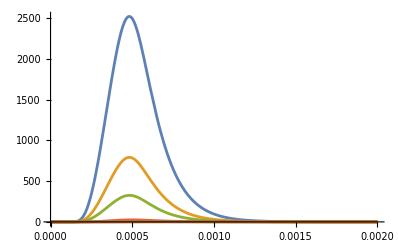

```mathematica
If[CaPlot==1,
Plot[
Evaluate[
Table[10^6/10^3*Ca[i][t], {i, {2,5,10,50,shells/2,shells}}] /. sol], {t, 0., TimeWindow}, PlotRange -> All]] (*in µM*)
```

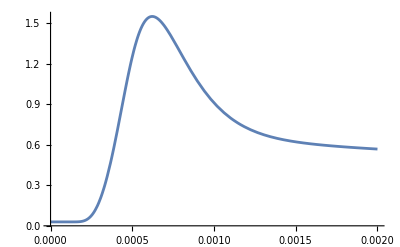

```mathematica
If[AvCaPlot==1,
Plot[Evaluate[10^6/10^3*AvCa/.sol],{t,0,TimeWindow},PlotRange->All]] (*in µM*)
```

## Release

### Edit

```mathematica
o=1;
u=shells;
Syt1prim=1; (*new Syt1 priming model*)
Syt1n=0; (*new Syt1 model*)
```

### Parmeters

```mathematica
If[Syt1prim==1,
R1size=1.;
Vtotal=1.;
n=5;
Km=20.*10^-3;
v=6000.;
vb=0.;
kOffV=10000.;
kOnV=1.*10^5;
a=4;
g=4000.;
]

If[Syt1n==1,
Vtotal=1.;
kOffV=10000.;
kOnV=1.*10^5;
a=4.;
g=5900.;
]
```

### Resting conditions

```mathematica
(*Vtotal=1.0;
If[Schnegg==0,
RuheVL=Join[
(* t=0 equations *)
{RestVL[0]==Vtotal},
{RestCaVL[0]==0},
{RestCa2VL[0]==0},
{RestCa3VL[0]==0},
{RestCa4VL[0]==0},
{RestCa5VL[0]==0},

(* f' equations *)
{RestVL'[x]==-(RestCaVL'[x]+RestCa2VL'[x]+RestCa3VL'[x]+RestCa4VL'[x]+RestCa5VL'[x])},
{RestCaVL'[x]==5*kOnVL*CaRest*RestVL[x] - kOffVL *RestCaVL[x]},
{RestCa2VL'[x]==4*kOnVL*CaRest* RestCaVL[x] - 2*bL*kOffVL *RestCa2VL[x]},
{RestCa3VL'[x]==3*kOnVL*CaRest*RestCa2VL[x] - 3*bL^2 *kOffVL *RestCa3VL[x]},
{RestCa4VL'[x]==2*kOnVL*CaRest* RestCa3VL[x] - 4*bL^3*kOffVL *RestCa4VL[x]},
{RestCa5VL'[x]==kOnVL*CaRest* RestCa4VL[x] - 5*bL^4*kOffVL *RestCa5VL[x]}
];

solVL := NDSolve[RuheVL,{RestVL,RestCaVL,RestCa2VL,RestCa3VL,RestCa4VL,RestCa5VL},{x,0.,1.}]; 

IniVL = Extract[RestVL[1.]/.solVL,1];
IniCaVL = Extract[RestCaVL[1.]/.solVL,1];
IniCa2VL = Extract[RestCa2VL[1.]/.solVL,1];
IniCa3VL = Extract[RestCa3VL[1.]/.solVL,1];
IniCa4VL = Extract[RestCa4VL[1.]/.solVL,1];
IniCa5VL = Extract[RestCa5VL[1.]/.solVL,1];
]

If[Schnegg==1,
RuheV=Join[
(* t=0 equations *)
{RestV[0]==Vtotal},
{RestCaV[0]==0},
{RestCa2V[0]==0},
{RestCa3V[0]==0},
{RestCa4V[0]==0},
{RestCa5V[0]==0},

(* f' equations *)
{RestV'[x]==-(RestCaV'[x]+RestCa2V'[x]+RestCa3V'[x]+RestCa4V'[x]+RestCa5V'[x])},
{RestCaV'[x]==5*kOnV*CaRest*RestV[x] - kOffV *RestCaV[x]},
{RestCa2V'[x]==4*kOnV*CaRest* RestCaV[x] - 2*b*kOffV *RestCa2V[x]},
{RestCa3V'[x]==3*kOnV*CaRest*RestCa2V[x] - 3*b^2 *kOffV *RestCa3V[x]},
{RestCa4V'[x]==2*kOnV*CaRest* RestCa3V[x] - 4*b^3*kOffV *RestCa4V[x]},
{RestCa5V'[x]==kOnV*CaRest* RestCa4V[x] - 5*b^4*kOffV *RestCa5V[x]}
];

solV := NDSolve[RuheV,{RestV,RestCaV,RestCa2V,RestCa3V,RestCa4V,RestCa5V},{x,0.,1.}]; 

IniV = Extract[RestV[1.]/.solV,1];
IniCaV = Extract[RestCaV[1.]/.solV,1];
IniCa2V = Extract[RestCa2V[1.]/.solV,1];
IniCa3V = Extract[RestCa3V[1.]/.solV,1];
IniCa4V = Extract[RestCa4V[1.]/.solV,1];
IniCa5V = Extract[RestCa5V[1.]/.solV,1];
]*)
```

### Sensor models and solving

```mathematica
ClearAll[Fusion,VarsSensor,Eqns1,Vars1,sol1,FusRate]

If[Syt1prim==1,
Fusion:=Join[
(* t=0 equations *)

Table[{R1[i][0]==R1size},{i,o,u}],
Table[{V[i][0]==Vtotal},{i,o,u}],
Table[{CaV[i][0]==0},{i,o,u}],
Table[{Ca2V[i][0]==0},{i,o,u}],
Table[{Ca3V[i][0]==0},{i,o,u}],
Table[{Ca4V[i][0]==0},{i,o,u}],
Table[{Ca5V[i][0]==0},{i,o,u}],
Table[{Fus[i][0]==0},{i,o,u}],

Table[R1[i]'[t]==-v*(Ca[i][t]^n/(Ca[i][t]^n+Km^n))*R1[i][t]+vb*V[i][t],{i,o,u}],

Table[{V[i]'[t]==-5*kOnV*Ca[i][t]* V[i][t] + kOffV *CaV[i][t]+v*(Ca[i][t]^n/(Ca[i][t]^n+Km^n))*R1[i][t]-vb*V[i][t]},{i,o,u}],

Table[{CaV[i]'[t]==5*kOnV*Ca[i][t]* V[i][t] - kOffV *CaV[i][t]-4*a kOnV*Ca[i][t]* CaV[i][t] +2* kOffV *Ca2V[i][t]},{i,o,u}],
Table[{Ca2V[i]'[t]==4*a kOnV*Ca[i][t]* CaV[i][t] -2* kOffV *Ca2V[i][t]-3*a^2 kOnV*Ca[i][t]* Ca2V[i][t] + 3*kOffV *Ca3V[i][t]},{i,o,u}],
Table[{Ca3V[i]'[t]==3*a^2 kOnV*Ca[i][t]* Ca2V[i][t] - 3*kOffV *Ca3V[i][t]-2*a^3 kOnV*Ca[i][t]* Ca3V[i][t] + 4*kOffV *Ca4V[i][t]},{i,o,u}],
Table[{Ca4V[i]'[t]==2*a^3 kOnV*Ca[i][t]* Ca3V[i][t] - 4*kOffV *Ca4V[i][t]-a^4 kOnV*Ca[i][t]* Ca4V[i][t] + 5*kOffV *Ca5V[i][t]},{i,o,u}],
Table[{Ca5V[i]'[t]==a^4 kOnV*Ca[i][t]* Ca4V[i][t] - 5*kOffV *Ca5V[i][t]-Fus[i]'[t]},{i,o,u}],
Table[{Fus[i]'[t]==g*Ca5V[i][t]},{i,o,u}]
]];

If[Syt1n==1,
Fusion:=Join[
(* t=0 equations *)

Table[{V[i][0]==Vtotal},{i,o,u}],
Table[{CaV[i][0]==0},{i,o,u}],
Table[{Ca2V[i][0]==0},{i,o,u}],
Table[{Ca3V[i][0]==0},{i,o,u}],
Table[{Ca4V[i][0]==0},{i,o,u}],
Table[{Ca5V[i][0]==0},{i,o,u}],
Table[{Fus[i][0]==0},{i,o,u}],

Table[{V[i]'[t]==-5*kOnV*Ca[i][t]* V[i][t] + kOffV *CaV[i][t]},{i,o,u}],

Table[{CaV[i]'[t]==5*kOnV*Ca[i][t]* V[i][t] - kOffV *CaV[i][t]-4*a kOnV*Ca[i][t]* CaV[i][t] +2* kOffV *Ca2V[i][t]},{i,o,u}],
Table[{Ca2V[i]'[t]==4*a kOnV*Ca[i][t]* CaV[i][t] -2* kOffV *Ca2V[i][t]-3*a^2 kOnV*Ca[i][t]* Ca2V[i][t] + 3*kOffV *Ca3V[i][t]},{i,o,u}],
Table[{Ca3V[i]'[t]==3*a^2 kOnV*Ca[i][t]* Ca2V[i][t] - 3*kOffV *Ca3V[i][t]-2*a^3 kOnV*Ca[i][t]* Ca3V[i][t] + 4*kOffV *Ca4V[i][t]},{i,o,u}],
Table[{Ca4V[i]'[t]==2*a^3 kOnV*Ca[i][t]* Ca3V[i][t] - 4*kOffV *Ca4V[i][t]-a^4 kOnV*Ca[i][t]* Ca4V[i][t] + 5*kOffV *Ca5V[i][t]},{i,o,u}],
Table[{Ca5V[i]'[t]==a^4 kOnV*Ca[i][t]* Ca4V[i][t] - 5*kOffV *Ca5V[i][t]-Fus[i]'[t]},{i,o,u}],
Table[{Fus[i]'[t]==g*Ca5V[i][t]},{i,o,u}]
]];

If[Syt1prim==1,
Fusion=Flatten[Fusion];

VarsSensor = 
Join[
Table[{R1[i],V[i],CaV[i],Ca2V[i],Ca3V[i],Ca4V[i],Ca5V[i],Fus[i]},{i,o,u}]];

VarsSensor=Flatten[VarsSensor];
Eqns1 =Flatten[Join[Eqns,{Fusion}]];
Vars1=Flatten[Join[Vars, {VarsSensor}]];
sol1 = NDSolve[Eqns1,Vars1,{t,0.,TimeWindow},Method->{"EquationSimplification"->"Residual"}];

If[DiscreteDist==1,
FusRate=Evaluate[Table[(Fus[i]'[t]),{i,DistList}]/.sol1];
,
FusRate=Evaluate[Table[(Fus[i]'[t]),{i,o,u,1}]/.sol1];
]

]


If[Syt1n==1,
Fusion=Flatten[Fusion];

VarsSensor = 
Join[
Table[{V[i],CaV[i],Ca2V[i],Ca3V[i],Ca4V[i],Ca5V[i],Fus[i]},{i,o,u}]];

VarsSensor=Flatten[VarsSensor];
Eqns1 =Flatten[Join[Eqns,{Fusion}]];
Vars1=Flatten[Join[Vars, {VarsSensor}]];
sol1 = NDSolve[Eqns1,Vars1,{t,0.,TimeWindow},Method->{"EquationSimplification"->"Residual"}];

If[DiscreteDist==1,
FusRate=Evaluate[Table[(Fus[i]'[t]),{i,DistList}]/.sol1];
,
FusRate=Evaluate[Table[(Fus[i]'[t]),{i,o,u,1}]/.sol1];
]

]
```

### Plotting

```mathematica
If[Syt1prim==1,Print["New Syt1 Priming Model"]]
If[Syt1n==1,Print["New Syt1 Model"]]

If[FusPlot==1,
p1=Plot[FusRate,{t,0,TimeWindow},PlotRange->All,AxesLabel->"Vesicle/s",PlotLabel->"Release Rate"]
]
```

New Syt1 Priming Model

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]

### Calculating pr

1.×10^-9 | 1.
2.×10^-9 | 0.99324
3.×10^-9 | 0.987559
4.×10^-9 | 0.98236
5.×10^-9 | 0.977401
6.×10^-9 | 0.972557
7.×10^-9 | 0.967754
8.×10^-9 | 0.962944
9.×10^-9 | 0.95809
1.×10^-8 | 0.953166
1.1×10^-8 | 0.94815
1.2×10^-8 | 0.943023
1.3×10^-8 | 0.937768
1.4×10^-8 | 0.93237
1.5×10^-8 | 0.926815
1.6×10^-8 | 0.921089
1.7×10^-8 | 0.915179
1.8×10^-8 | 0.909071
1.9×10^-8 | 0.902751
2.×10^-8 | 0.896205
2.1×10^-8 | 0.889417
2.2×10^-8 | 0.882373
2.3×10^-8 | 0.875054
2.4×10^-8 | 0.867441
2.5×10^-8 | 0.859514
2.6×10^-8 | 0.851249
2.7×10^-8 | 0.84262
2.8×10^-8 | 0.833598
2.9×10^-8 | 0.824149
3.×10^-8 | 0.814238
3.1×10^-8 | 0.803825
3.2×10^-8 | 0.79287
3.3×10^-8 | 0.781331
3.4×10^-8 | 0.769166
3.5×10^-8 | 0.756337
3.6×10^-8 | 0.742811
3.7×10^-8 | 0.728558
3.8×10^-8 | 0.713561
3.9×10^-8 | 0.69781
4.×10^-8 | 0.681305
4.1×10^-8 | 0.664063
4.2×10^-8 | 0.646111
4.3×10^-8 | 0.62749
4.4×10^-8 | 0.608257
4.5×10^-8 | 0.58848
4.6×10^-8 | 0.568243
4.7×10^-8 | 0.547641
4.8×10^-8 | 0.526781
4.9×10^-8 | 0.505778
5.×10^-8 | 0.484755
5.1×10^-8 | 0.46384
5.2×10^-8 | 0.443159
5.3×10^-8 | 0.422837
5.4×10^-8 | 0.402988
5.5×10^-8 | 0.383716
5.6×10^-8 | 0.365109
5.7×10^-8 | 0.347234
5.8×10^-8 | 0.330142
5.9×10^-8 | 0.313861
6.×10^-8 | 0.2984
6.1×10^-8 | 0.283754
6.2×10^-8 | 0.269903
6.3×10^-8 | 0.256816
6.4×10^-8 | 0.244455
6.5×10^-8 | 0.232778
6.6×10^-8 | 0.221742
6.7×10^-8 | 0.211303
6.8×10^-8 | 0.201419
6.9×10^-8 | 0.192049
7.×10^-8 | 0.183159
7.1×10^-8 | 0.174712
7.2×10^-8 | 0.166681
7.3×10^-8 | 0.159037
7.4×10^-8 | 0.151756
7.5×10^-8 | 0.144815
7.6×10^-8 | 0.138197
7.7×10^-8 | 0.131882
7.8×10^-8 | 0.125855
7.9×10^-8 | 0.120102
8.×10^-8 | 0.114608
8.1×10^-8 | 0.109363
8.2×10^-8 | 0.104355
8.3×10^-8 | 0.0995721
8.4×10^-8 | 0.0950056
8.5×10^-8 | 0.0906457
8.6×10^-8 | 0.0864837
8.7×10^-8 | 0.0825109
8.8×10^-8 | 0.0787193
8.9×10^-8 | 0.0751012
9.×10^-8 | 0.0716491
9.1×10^-8 | 0.0683558
9.2×10^-8 | 0.0652145
9.3×10^-8 | 0.0622186
9.4×10^-8 | 0.0593617
9.5×10^-8 | 0.0566376
9.6×10^-8 | 0.0540406
9.7×10^-8 | 0.051565
9.8×10^-8 | 0.0492052
9.9×10^-8 | 0.0469561
1.×10^-7 | 0.0448126
1.01×10^-7 | 0.0427699
1.02×10^-7 | 0.0408234
1.03×10^-7 | 0.0389686
1.04×10^-7 | 0.0372012
1.05×10^-7 | 0.0355172
1.06×10^-7 | 0.0339127
1.07×10^-7 | 0.0323839
1.08×10^-7 | 0.0309272
1.09×10^-7 | 0.0295393
1.1×10^-7 | 0.0282168
1.11×10^-7 | 0.0269567
1.12×10^-7 | 0.0257559
1.13×10^-7 | 0.0246116
1.14×10^-7 | 0.0235211
1.15×10^-7 | 0.0224819
1.16×10^-7 | 0.0214914
1.17×10^-7 | 0.0205473
1.18×10^-7 | 0.0196474
1.19×10^-7 | 0.0187895
1.2×10^-7 | 0.0179716
1.21×10^-7 | 0.0171918
1.22×10^-7 | 0.0164483
1.23×10^-7 | 0.0157392
1.24×10^-7 | 0.015063
1.25×10^-7 | 0.014418
1.26×10^-7 | 0.0138028
1.27×10^-7 | 0.0132158
1.28×10^-7 | 0.0126558
1.29×10^-7 | 0.0121215
1.3×10^-7 | 0.0116116
1.31×10^-7 | 0.0111249
1.32×10^-7 | 0.0106603
1.33×10^-7 | 0.0102168
1.34×10^-7 | 0.00979341
1.35×10^-7 | 0.00938909
1.36×10^-7 | 0.00900297
1.37×10^-7 | 0.00863418
1.38×10^-7 | 0.00828191
1.39×10^-7 | 0.00794535
1.4×10^-7 | 0.00762378
1.41×10^-7 | 0.00731649
1.42×10^-7 | 0.0070228
1.43×10^-7 | 0.00674207
1.44×10^-7 | 0.0064737
1.45×10^-7 | 0.0062171
1.46×10^-7 | 0.00597173
1.47×10^-7 | 0.00573707
1.48×10^-7 | 0.00551261
1.49×10^-7 | 0.00529788
1.5×10^-7 | 0.00509243
1.51×10^-7 | 0.00489584
1.52×10^-7 | 0.00470769
1.53×10^-7 | 0.0045276
1.54×10^-7 | 0.0043552
1.55×10^-7 | 0.00419013
1.56×10^-7 | 0.00403207
1.57×10^-7 | 0.00388069
1.58×10^-7 | 0.00373569
1.59×10^-7 | 0.00359678
1.6×10^-7 | 0.00346368
1.61×10^-7 | 0.00333614
1.62×10^-7 | 0.00321391
1.63×10^-7 | 0.00309674
1.64×10^-7 | 0.00298441
1.65×10^-7 | 0.00287671
1.66×10^-7 | 0.00277343
1.67×10^-7 | 0.00267437
1.68×10^-7 | 0.00257934
1.69×10^-7 | 0.00248818
1.7×10^-7 | 0.00240071
1.71×10^-7 | 0.00231676
1.72×10^-7 | 0.00223619
1.73×10^-7 | 0.00215884
1.74×10^-7 | 0.00208458
1.75×10^-7 | 0.00201328
1.76×10^-7 | 0.00194479
1.77×10^-7 | 0.00187902
1.78×10^-7 | 0.00181582
1.79×10^-7 | 0.00175511
1.8×10^-7 | 0.00169677
1.81×10^-7 | 0.00164069
1.82×10^-7 | 0.00158679
1.83×10^-7 | 0.00153497
1.84×10^-7 | 0.00148514
1.85×10^-7 | 0.00143722
1.86×10^-7 | 0.00139113
1.87×10^-7 | 0.0013468
1.88×10^-7 | 0.00130414
1.89×10^-7 | 0.00126309
1.9×10^-7 | 0.00122359
1.91×10^-7 | 0.00118557
1.92×10^-7 | 0.00114896
1.93×10^-7 | 0.00111371
1.94×10^-7 | 0.00107977
1.95×10^-7 | 0.00104708
1.96×10^-7 | 0.00101559
1.97×10^-7 | 0.000985247
1.98×10^-7 | 0.000956012
1.99×10^-7 | 0.000927837
2.×10^-7 | 0.000900679
2.01×10^-7 | 0.000874499
2.02×10^-7 | 0.000849256
2.03×10^-7 | 0.000824914
2.04×10^-7 | 0.000801436
2.05×10^-7 | 0.000778789
2.06×10^-7 | 0.00075694
2.07×10^-7 | 0.000735858
2.08×10^-7 | 0.000715511
2.09×10^-7 | 0.000695873
2.1×10^-7 | 0.000676914
2.11×10^-7 | 0.000658609
2.12×10^-7 | 0.000640933
2.13×10^-7 | 0.000623861
2.14×10^-7 | 0.000607371
2.15×10^-7 | 0.000591439
2.16×10^-7 | 0.000576044
2.17×10^-7 | 0.000561167
2.18×10^-7 | 0.000546787
2.19×10^-7 | 0.000532886
2.2×10^-7 | 0.000519446
2.21×10^-7 | 0.000506449
2.22×10^-7 | 0.00049388
2.23×10^-7 | 0.000481721
2.24×10^-7 | 0.000469958
2.25×10^-7 | 0.000458576
2.26×10^-7 | 0.000447562
2.27×10^-7 | 0.000436901
2.28×10^-7 | 0.000426581
2.29×10^-7 | 0.000416589
2.3×10^-7 | 0.000406914
2.31×10^-7 | 0.000397544
2.32×10^-7 | 0.000388468
2.33×10^-7 | 0.000379675
2.34×10^-7 | 0.000371156
2.35×10^-7 | 0.0003629
2.36×10^-7 | 0.000354899
2.37×10^-7 | 0.000347143
2.38×10^-7 | 0.000339623
2.39×10^-7 | 0.000332332
2.4×10^-7 | 0.000325261
2.41×10^-7 | 0.000318403
2.42×10^-7 | 0.00031175
2.43×10^-7 | 0.000305295
2.44×10^-7 | 0.000299032
2.45×10^-7 | 0.000292954
2.46×10^-7 | 0.000287054
2.47×10^-7 | 0.000281326
2.48×10^-7 | 0.000275765
2.49×10^-7 | 0.000270366
2.5×10^-7 | 0.000265121
2.51×10^-7 | 0.000260028
2.52×10^-7 | 0.000255079
2.53×10^-7 | 0.000250271
2.54×10^-7 | 0.000245599
2.55×10^-7 | 0.000241059
2.56×10^-7 | 0.000236645
2.57×10^-7 | 0.000232355
2.58×10^-7 | 0.000228183
2.59×10^-7 | 0.000224127
2.6×10^-7 | 0.000220182
2.61×10^-7 | 0.000216344
2.62×10^-7 | 0.000212611
2.63×10^-7 | 0.00020898
2.64×10^-7 | 0.000205446
2.65×10^-7 | 0.000202007
2.66×10^-7 | 0.000198659
2.67×10^-7 | 0.000195401
2.68×10^-7 | 0.000192228
2.69×10^-7 | 0.000189139
2.7×10^-7 | 0.000186131
2.71×10^-7 | 0.000183201
2.72×10^-7 | 0.000180348
2.73×10^-7 | 0.000177568
2.74×10^-7 | 0.000174859
2.75×10^-7 | 0.00017222
2.76×10^-7 | 0.000169647
2.77×10^-7 | 0.00016714
2.78×10^-7 | 0.000164697
2.79×10^-7 | 0.000162314
2.8×10^-7 | 0.000159991
2.81×10^-7 | 0.000157726
2.82×10^-7 | 0.000155517
2.83×10^-7 | 0.000153362
2.84×10^-7 | 0.00015126
2.85×10^-7 | 0.00014921
2.86×10^-7 | 0.000147209
2.87×10^-7 | 0.000145257
2.88×10^-7 | 0.000143352
2.89×10^-7 | 0.000141492
2.9×10^-7 | 0.000139677
2.91×10^-7 | 0.000137905
2.92×10^-7 | 0.000136175
2.93×10^-7 | 0.000134486
2.94×10^-7 | 0.000132836
2.95×10^-7 | 0.000131225
2.96×10^-7 | 0.000129651
2.97×10^-7 | 0.000128114
2.98×10^-7 | 0.000126612
2.99×10^-7 | 0.000125145
3.×10^-7 | 0.000123711
3.01×10^-7 | 0.00012231
3.02×10^-7 | 0.00012094
3.03×10^-7 | 0.000119602
3.04×10^-7 | 0.000118293
3.05×10^-7 | 0.000117014
3.06×10^-7 | 0.000115763
3.07×10^-7 | 0.00011454
3.08×10^-7 | 0.000113344
3.09×10^-7 | 0.000112175
3.1×10^-7 | 0.000111031
3.11×10^-7 | 0.000109912
3.12×10^-7 | 0.000108817
3.13×10^-7 | 0.000107746
3.14×10^-7 | 0.000106698
3.15×10^-7 | 0.000105672
3.16×10^-7 | 0.000104669
3.17×10^-7 | 0.000103686
3.18×10^-7 | 0.000102725
3.19×10^-7 | 0.000101784
3.2×10^-7 | 0.000100862
3.21×10^-7 | 0.0000999601
3.22×10^-7 | 0.0000990767
3.23×10^-7 | 0.0000982116
3.24×10^-7 | 0.0000973643
3.25×10^-7 | 0.0000965343
3.26×10^-7 | 0.0000957214
3.27×10^-7 | 0.0000949249
3.28×10^-7 | 0.0000941445
3.29×10^-7 | 0.0000933799
3.3×10^-7 | 0.0000926305
3.31×10^-7 | 0.0000918961
3.32×10^-7 | 0.0000911762
3.33×10^-7 | 0.0000904705
3.34×10^-7 | 0.0000897786
3.35×10^-7 | 0.0000891001
3.36×10^-7 | 0.0000884348
3.37×10^-7 | 0.0000877823
3.38×10^-7 | 0.0000871422
3.39×10^-7 | 0.0000865142
3.4×10^-7 | 0.0000858981
3.41×10^-7 | 0.0000852935
3.42×10^-7 | 0.0000847
3.43×10^-7 | 0.0000841175
3.44×10^-7 | 0.0000835456
3.45×10^-7 | 0.000082984
3.46×10^-7 | 0.0000824325
3.47×10^-7 | 0.0000818907
3.48×10^-7 | 0.0000813584
3.49×10^-7 | 0.0000808353
3.5×10^-7 | 0.0000803211
3.51×10^-7 | 0.0000798157
3.52×10^-7 | 0.0000793187
3.53×10^-7 | 0.0000788298
3.54×10^-7 | 0.0000783488
3.55×10^-7 | 0.0000778755
3.56×10^-7 | 0.0000774096
3.57×10^-7 | 0.0000769509
3.58×10^-7 | 0.000076499
3.59×10^-7 | 0.0000760538
3.6×10^-7 | 0.0000756151
3.61×10^-7 | 0.0000751825
3.62×10^-7 | 0.0000747558
3.63×10^-7 | 0.0000743348
3.64×10^-7 | 0.0000739193
3.65×10^-7 | 0.0000735089
3.66×10^-7 | 0.0000731035
3.67×10^-7 | 0.0000727028
3.68×10^-7 | 0.0000723066
3.69×10^-7 | 0.0000719146
3.7×10^-7 | 0.0000715265
3.71×10^-7 | 0.0000711422
3.72×10^-7 | 0.0000707613
3.73×10^-7 | 0.0000703837
3.74×10^-7 | 0.0000700089
3.75×10^-7 | 0.0000696369
3.76×10^-7 | 0.0000692673
3.77×10^-7 | 0.0000688999
3.78×10^-7 | 0.0000685344
3.79×10^-7 | 0.0000681705
3.8×10^-7 | 0.000067808
3.81×10^-7 | 0.0000674465
3.82×10^-7 | 0.0000670858
3.83×10^-7 | 0.0000667256
3.84×10^-7 | 0.0000663657
3.85×10^-7 | 0.0000660056
3.86×10^-7 | 0.0000656451
3.87×10^-7 | 0.0000652839
3.88×10^-7 | 0.0000649216
3.89×10^-7 | 0.0000645581
3.9×10^-7 | 0.0000641928
3.91×10^-7 | 0.0000638255
3.92×10^-7 | 0.0000634559
3.93×10^-7 | 0.0000630835
3.94×10^-7 | 0.0000627081
3.95×10^-7 | 0.0000623293
3.96×10^-7 | 0.0000619466
3.97×10^-7 | 0.0000615598
3.98×10^-7 | 0.0000611684
3.99×10^-7 | 0.0000607721
4.×10^-7 | 0.0000603705

New Syt1 Priming Model

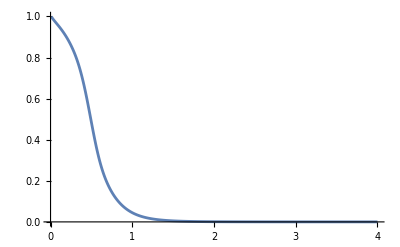

```mathematica
If[CalPr==1,
If[DiscreteDist==1,
dist=10^9*ds*DistList,
dist=Table[x*ds,{x,o,u}];]
]

If[CalPr==1,
pr1=NIntegrate[{FusRate},{t,startT,0.002}];
	pr1=Flatten[pr1];
If[Syt1prim==1,pr1/=pr1[[1]],pr1];               (*This normalization is required since there are 2 vesicles, 1 in R1, 1 in V1!*)
	  Row[pr1," "];
TableForm[Transpose[{dist,pr1}]]
]

If[CalCaList==1,
CaList={};
For[i=o,i≤u,i+=1,
w=FindMaximum[Evaluate[(10^3*Ca[i][t])/.sol],{t,0,TimeWindow}];
AppendTo[CaList,First[w]]
];
TableForm[CaList]
]

If[Syt1prim==1,Print["New Syt1 Priming Model"]]
If[Syt1n==1,Print["New Syt1 Model"]]
If[CalPr==1,
prPlot=Join[{dist,pr1}];
prPlot=Transpose[prPlot];
ListLinePlot[prPlot,PlotRange->All]]
```

## Plotting Ca and Controls

```mathematica
(*Plot[Evaluate[(10^3*Ca[11][t])/.sol],{t,0,TimeWindow},PlotRange->All]
*)
```

```mathematica
(*Plot[Evaluate[Table[(R1[i][t]),{i,{3}}]/.sol1],{t,0,TimeWindow}]
Plot[Evaluate[Table[(V[i][t]),{i,{3}}]/.sol1],{t,0,TimeWindow}]
Plot[Evaluate[Table[(Fus[i][t]),{i,{3}}]/.sol1],{t,0,TimeWindow}]
Plot[Evaluate[(Fus[11]'[t])/1.93/.sol1],{t,0,TimeWindow},(*PlotRange->{All,{All,2000}},*)PlotRange->All]*)
```

## Plots pv vs dist

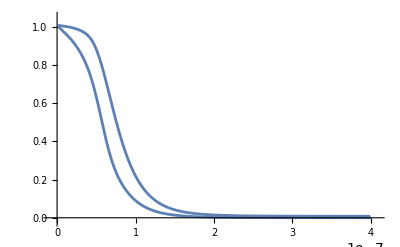

-Graphics-